# On the sign changes of

```mathematica
ExpressionCell[
Row[{
Spacer[190],
Column[{Spacer[{1,0}],Framed[BarcodeImage["arxiv.org/abs/2408.10399",{"Aztec",8},380],Background->White]}],
Spacer[20],Column[{Spacer[{1,20}],"M. Grześkowiak, J. Kaczorowski,","Ł. Pańkowski, M. Radziejewski","(Adam Mickiewicz University, Poznań)"}]
}],FontSize->26,FontFamily->"Roboto Slab",FontColor->White,Magnification->1.5]
```

-Graphics-
M. Grześkowiak, J. Kaczorowski,
Ł. Pańkowski, M. Radziejewski
(Adam Mickiewicz University, Poznań)

To run the presentation:
1. Enable dynamic, potentially unsafe content, by clicking on the button “Enable dynamics” displayed with a warning.
2. Run the initialization code using Evaluation/Evaluate Initialization Cells (this takes about 6 minutes on Macbook M1 Pro).
3. Hide the input cells by double-clicking the output cell brackets. This has to be done only for two output cells that have to be recomputed on opening the notebook:
   • V(T),
   • the second one of the plots with a large, green area,
      described “Conjecture: Density equals vol A.” (in this case it is sometime necessary to first re-compute the plot by evaluating the input).
4. Click the button “Start Presentation”.

## Error term in the PNT

Von Mangoldt function:

Λ(n)==Piecewise[{{log(p),, n==p^k,}, {0, otherwise.}}]

Chebyshev function:

ψ(x)==∑_(n≤x) Λ(n)

Prime Number Theorem:

ψ(x)==x+O(…)

Error term:

ψ(x)-x

➔

## Sign changes of the error term

```mathematica
cN=21; (* N in the paper *)
epsilon=3.32`100×10^-13; (* Obtained from Algorithm 1 for the given N. *)
precision = 100;
numZeros=10000; 
$MaxExtraPrecision=2*precision;
Parallelize[imZero=Table[N[Im[ZetaZero[k]],{Infinity,precision+10}],{k,1,numZeros}]];
gamma[n_]:=imZero[[n+1]];
omega[n_]:=gamma[n]-gamma[0];
rho[n_]:=1/2+I gamma[n];
cFN[cN_,z_]:=1+rho[0]Sum[Exp[I(gamma[n]-gamma[0])z]/rho[n],{n,cN}];
error=10^(5-precision);  (* For basic upward rounding. *)
aUpperBound[n_]:=(Abs[rho[0]]+error)/(Abs[rho[n]]-error);
(* The upper bound for R_N(y). *)
cRN[cNpar_,y_]:=
Module[{cT1=(gamma[9998]+gamma[9999])/2},Sum[aUpperBound[n] Exp[y(error-(gamma[n]-gamma[0]))],{n,cNpar+1,9998}]+
((Abs[rho[0]]+error)Exp[y(gamma[0]-cT1+error)]/(cT1-error))(Log[cT1+error](4+1/(2 Pi y))+2/(y(cT1-error)))];
cFNeta[z_]:=1-Sum[Abs[rho[0]/rho[n]]Exp[I omega[n]z],{n,1,cN}];
f[z_]:=-Sum[I omega[n] Abs[rho[0]/rho[n]]Exp[I omega[n]z],{n,1,cN}];
delta=132737/10^6;
y0=468918/10^7;
y1=14/100;
m=4800;
z1=Join[
Table[4 t delta+y0 I,{t,0,1/8,1/m}],
Table[delta/2+(y0+4(t-1/8)(y1-y0)) I,{t,1/8+1/m,3/8,1/m}],
Table[-4(t-1/2)delta+y1 I,{t,3/8+1/m,5/8,1/m}],
Table[-delta/2+(y1+4(t-5/8)(y0-y1)) I,{t,5/8+1/m,7/8,1/m}],
Table[4(t-1)delta+y0 I,{t,7/8+1/m,1,1/m}]
]; (* i.e. z1[[1]],...,z[[m+1]] represent .
*)
(* The argument function, denoted as  in the paper, is called argFun[t] here. *)
argFunBreakpoints={0,1/32,1/8,3/16,3/8,1/2};
argFunValues={0,489819/10^6,185802/10^5,204829/10^5,290189/10^5,Pi};
argFun[t_]:=Simplify[Piecewise[Table[{(argFunValues[[j]]*(argFunBreakpoints[[j+1]]-t)+argFunValues[[j+1]]*(t-argFunBreakpoints[[j]]))/(argFunBreakpoints[[j+1]]-argFunBreakpoints[[j]]),argFunBreakpoints[[j]]<=t<=argFunBreakpoints[[j+1]]},{j,5}]]];
alpha=Join[
Table[-N[Pi,precision]+argFun[(j-1/2)/m],{j,1,m/2}],
Table[N[Pi,precision] - argFun[(m+1/2-j)/m],{j,m/2+1,m}]
];
alpha=Join[{alpha[[m]]-2Pi},alpha,{2Pi+alpha[[1]]}]; (* i.e. alpha[[j+1]] represents  in the paper. *)
values=Table[cFNeta[z1[[j]]],{j,1,m}];
mSparse=120;
z1Sparse=Join[
Table[4 t delta+y0 I,{t,0,1/8,1/mSparse}],
Table[delta/2+(y0+4 (t-1/8) (y1-y0)) I,{t,1/8+1/mSparse,3/8,1/mSparse}],Table[-4 (t-1/2) delta+y1 I,{t,3/8+1/mSparse,5/8,1/mSparse}],Table[-delta/2+(y1+4 (t-5/8) (y0-y1)) I,{t,5/8+1/mSparse,7/8,1/mSparse}],Table[4 (t-1) delta+y0 I,{t,7/8+1/mSparse,1,1/mSparse}]
];
valuesSparse=Table[cFNeta[z1Sparse[[j]]],{j,1,mSparse}];
rSparse=Table[cRN[cN,Im[z1Sparse[[j]]]],{j,mSparse}];
alphaSparse=Join[
Table[-N[Pi]+N[argFun[(j-1)/mSparse]],{j,1,mSparse/2}],
Table[N[Pi] - N[argFun[(mSparse+1-j)/mSparse]],{j,mSparse/2+1,mSparse}]
];
b=Table[(1/2)Abs[z1[[j]]-z1[[j+1]]],{j,1,m}];
xPrime=Table[Min[Re[z1[[j]]],Re[z1[[j+1]]]],{j,1,m}]; (*  *)
xBis=Table[Max[Re[z1[[j]]],Re[z1[[j+1]]]],{j,1,m}]; (*  — we use the Latin "bis" instead of "double prime" *)
y=Table[Min[Im[z1[[j]]],Im[z1[[j+1]]]],{j,1,m}];
cM=Table[Sum[Abs[rho[0]/rho[n]]omega[n]^2Exp[-omega[n]y[[j]]],{n,1,cN}],{j,1,m}];
pi=N[Pi,precision];
yUnique=Union[y];
cRNLookup=Association[Table[yUnique[[j]]->cRN[cN,yUnique[[j]]],{j,1,Length[yUnique]}]];
u=Table[Min[
Re[cFNeta[z1[[j]]]Exp[-I alpha[[j+1]]]]+Min[0,Re[b[[j]]f[z1[[j]]]Exp[-I alpha[[j+1]]]]],
Re[cFNeta[z1[[j+1]]]Exp[-I alpha[[j+1]]]]+Min[0,-Re[b[[j]]f[z1[[j+1]]]Exp[-I alpha[[j+1]]]]]
]-b[[j]]^2cM[[j]]/2-cRNLookup[y[[j]]],
{j,1,m}];
norm[x_]:=Min[x-Floor[x],Ceiling[x]-x];
betaPrime=Table[Table[
pi+omega[n]xPrime[[j]]-alpha[[j+1]],
{j,1,m}],{n,1,cN}];
betaBis=Table[Table[
pi+omega[n]xBis[[j]]-alpha[[j+1]],
{j,1,m}],{n,1,cN}];
phiPrime=Table[Table[
Piecewise[{
{0,Ceiling[betaPrime[[n]][[j]]/(2pi)]<=Floor[betaBis[[n]][[j]]/(2pi)]},
{2pi Min[norm[betaPrime[[n]][[j]]/(2pi)],norm[betaBis[[n]][[j]]/(2pi)]],Ceiling[1/2+betaPrime[[n]][[j]]/(2pi)]<=Floor[1/2+betaBis[[n]][[j]]/(2pi)]}
},
2pi Min[norm[betaPrime[[n]][[j]]/(2pi)],norm[betaBis[[n]][[j]]/(2pi)]]
],
{j,1,m}],{n,1,cN}];
phiBis=Table[Table[
Piecewise[{
{2pi Max[norm[betaPrime[[n]][[j]]/(2pi)],norm[betaBis[[n]][[j]]/(2pi)]],Ceiling[betaPrime[[n]][[j]]/(2pi)]<=Floor[betaBis[[n]][[j]]/(2pi)]},
{pi,Ceiling[1/2+betaPrime[[n]][[j]]/(2pi)]<=Floor[1/2+betaBis[[n]][[j]]/(2pi)]}
},
2pi Max[norm[betaPrime[[n]][[j]]/(2pi)],norm[betaBis[[n]][[j]]/(2pi)]]
],
{j,1,m}],{n,1,cN}];
l=160;
ll=l;
epsilon=N[2*166*10^(-15),precision];
c=Table[Table[
Abs[rho[0]/rho[n]]/(u[[j]]Exp[omega[n]y[[j]]]
Piecewise[{
{Cos[phiBis[[n]][[j]]/2-phiPrime[[n]][[j]]/2],phiBis[[n]][[j]]<=pi/2},
{1,phiPrime[[n]][[j]]>=pi/2}
},Cos[pi/4-phiPrime[[n]][[j]]/2]
]),
{j,1,m}],{n,cN}];
For[n=1,n<=cN,n+=1,
c[[n]]=Join[{Max[Table[
(Abs[rho[0]/rho[n]]/(u[[j]]Exp[omega[n]y[[j]]]))
Piecewise[{
{0,phiBis[[n]][[j]]<pi/2},
{0,phiPrime[[n]][[j]]>pi/2}
},1/Cos[pi/4-phiPrime[[n]][[j]]/2]
],
{j,1,m}]]},c[[n]],c[[n]]];
];
phi=Table[Join[{pi/2},phiPrime[[n]],phiBis[[n]]],{n,cN}];
x=Table[Table[1/2-(3/2)epsilon,{k,1,l}],{n,cN}];
For[n=1,n<=cN,n+=1,
For[j=1,j<=Length[c[[n]]],j+=1,
maxk=Min[l,Ceiling[l c[[n]][[j]](Cos[phi[[n]][[j]]]+1)]];
For[k=1,k<=maxk,k+=1,
If[c[[n]][[j]](1+Cos[phi[[n]][[j]]])>k/l,
x[[n]][[k]]=Min[x[[n]][[k]],(ArcCos[Cos[phi[[n]][[j]]]-k/(l c[[n]][[j]])]-phi[[n]][[j]])/(2 pi)-(3/2)epsilon];
]
];
];
];
v[ϕ_,ψ_]:=Piecewise[{{Cos[ϕ]-Cos[ϕ+ψ],ϕ+ψ<=pi}},Cos[ϕ]+1];
w[n_,x_]:=Max[Table[c[[n]][[j]]v[phi[[n]][[j]],2 pi x],{j,Length[c[[n]]]}]];

xForVT=10000;
psi=Table[0,{k,xForVT}];
zeros={};
index=Table[0,{k,xForVT}];
For[k=2,k<=10000,k+=1,
psi[[k]]=psi[[k-1]]+N[MangoldtLambda[k]];
If[(psi[[k]]-k)(psi[[k-1]]-k+1)<0,
zeros=Join[zeros,{k-0.5}]
];
index[[k]]=Length[zeros]
];
t0=170;
t1=180;
ttt=1000;
Manipulate[Show[
LogLinearPlot[psi[[Floor[t]]]-t,{t,t0,Exp[tt]},ImageSize->900,PlotStyle->Thickness[0.002],Ticks->{{{Exp[tt],"   T"}}, None},TicksStyle->Directive[Large,Thick,Black],PlotRange->{{t0,ttt+t0},{-20,20}},PlotPoints->Floor[Exp[tt]],Epilog->Style[Text["V(T) = the number of sign changes up to T",{Log[500],17}],40]],ListLogLinearPlot[Table[{zeros[[j]],0},{j,index[[t0]]+1,index[[Floor[Exp[tt]]]]}],PlotStyle->{Darker[Red]}],
ListLogLinearPlot[{{Exp[tt],psi[[Floor[Exp[tt]]]]-Exp[tt]}},PlotStyle->{Darker[Blue],PointSize[0.02]}]
],{{tt,Log[t1],"T"},Log[t1],Log[ttt],ImageSize->800},Paneled->False]
```

A. E. Ingham (1936) has shown conditionally:

where

G. Pólya (1969):

.

Estimate

shown by J. Kaczorowski (1985).

Improvements based on -functions:

J. Kaczorowski (1991):

much more if RH fails,

so we can assume RH!

J. Kaczorowski (1996):  (proof unpublished)

T. Morrill, D. Platt and T. Trudgian (2022):

G., K., P. and R. (2024):

➔

## Outline of the method that we partially follow

## k-function and its zeros

J. Kaczorowski (1991):

+  the estimated mean density of
zeros of a so-called -function

Consider the non-trivial zeros of the Riemann zeta function:

```mathematica
t0=-1;t1=26;
Pane[
ParametricPlot[{sigma,t},{sigma,-0.5,7},{t,t0,t1},
ColorFunction->Function[{x,y},Module[
{v=Zeta[x+I y]},
Hue[
Arg[v]/(2Pi),
Sqrt[Sin[2 Pi(LogisticSigmoid[0.5Abs[v]]-0.5)]],
1-1/(1+1/(0.5Abs[v]))
]
]],ColorFunctionScaling->False,PlotPoints->{100,360},
Epilog->{{PointSize[0.02],White,Point[Table[{0.5,gamma[k]},{k,3,2}]]},Style[Text["",{3,gamma[0]}],40,White],Style[Text["",{3,gamma[1]}],40,White],Style[Text["",{3,gamma[2]}],40,White],{Dashed,Line[{{0,t0},{0,t1}}]},{Dashed,Line[{{1,t0},{1,t1}}]},Line[{{0.5,t0},{0.5,t1}}]},
Axes->None,GridLines->{{0,0.5,1},{}},ImageSize->600],
ImageSize->{600,700},Scrollbars->{False, False},ScrollPosition->{0, 2000}
]
```

-Graphics-

The series defining the -function

and the normalized -function (divided by the first term)

are absolutely convergent for , .

```mathematica
(*
We are using the function rasterizeBackground found here:
https://mathematica.stackexchange.com/questions/71870/rasterized-density-plot-with-vector-axes
modified slightly, to allow specifying different x and y resolution.
*)

ClearAll[rasterizeBackground];
Options[rasterizeBackground]={"TransparentBackground"->False,Antialiasing->False};
rasterizeBackground[g_Graphics,rs_:3000,OptionsPattern[]]:=Module[{raster,plotrange,rect},{raster,plotrange}=Reap[First@Rasterize[Show[g,Epilog->{},Prolog->{},PlotRangePadding->0,ImagePadding->0,ImageMargins->0,PlotLabel->None,FrameTicks->None,Frame->None,Axes->None,Ticks->None,PlotRangeClipping->False,Antialiasing->OptionValue[Antialiasing],GridLines->{Function[Sow[{##},"X"];None],Function[Sow[{##},"Y"];None]}],"Graphics",ImageSize->rs,Background->Replace[OptionValue["TransparentBackground"],{True->None,False->Automatic}]],_,#1->#2[[1]]&];
rect=Transpose[{"X","Y"}/. plotrange];
Graphics[raster/. Raster[data_,_,rest__]:>Raster[data,rect,rest],Options[g]]]

rasterizeBackground[g_,rs_:3000,OptionsPattern[]]:=g/. gr_Graphics:>rasterizeBackground[gr,rs]

Pane[
rasterizeBackground[ParametricPlot[{x,y},{x,-0.05,7},{y,0.001,0.1},
ColorFunction->Function[{x,y},Module[
{v=cFN[1000,x+I y]},
Hue[
Arg[v]/(2Pi),
Sqrt[Sin[2 Pi(LogisticSigmoid[0.5Abs[v]]-0.5)]],
1-1/(1+1/(0.5Abs[v]))
]
]],Axes->None,FrameTicks->{{Automatic,Automatic},{Table[0.1k,{k,0,70}],None}},ColorFunctionScaling->False,PlotPoints->{7000,100},
ImageSize->20000,PlotRangePadding->0],{7000,100}],
ImageSize->900,Scrollbars->{True, False}
]
```

-Graphics-

Density — what we believe and what we prove

Density ?

Maybe, but low-lying zeros are harder to confirm!

Every zero has infinitely many “copies”

positive density

Finite approximation:

,

To draw any conclusions from an approximation, you need to estimate the approximation error:

,

Two parts cut out from the plot above:

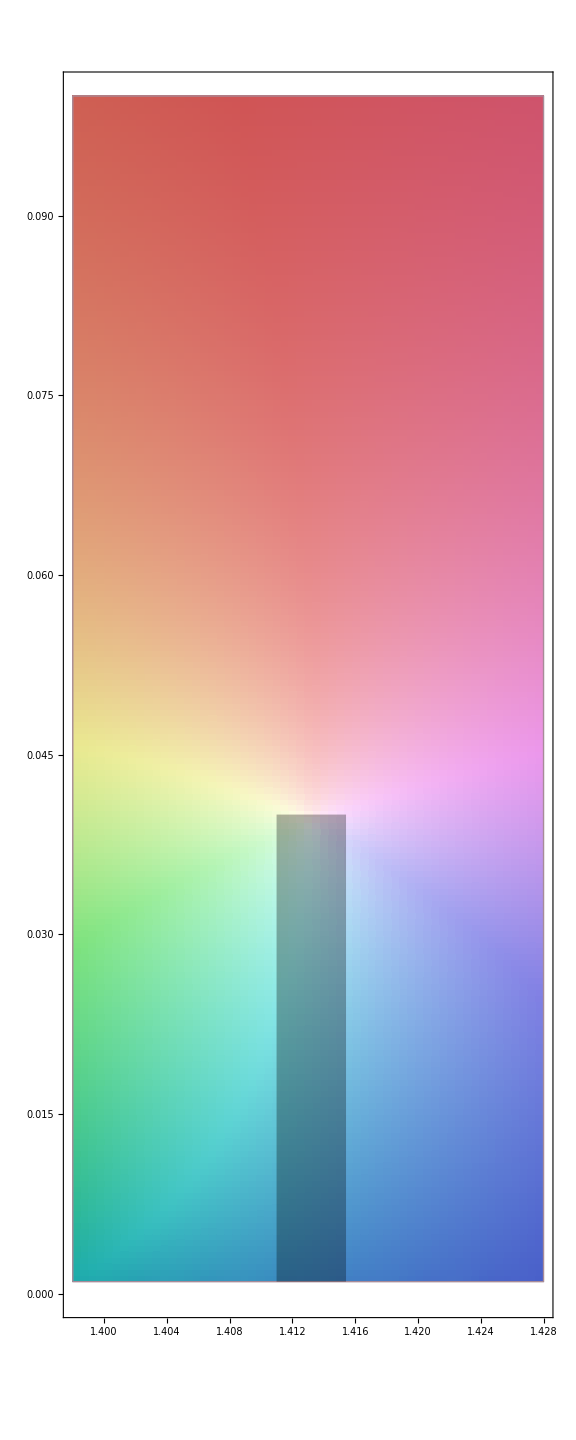
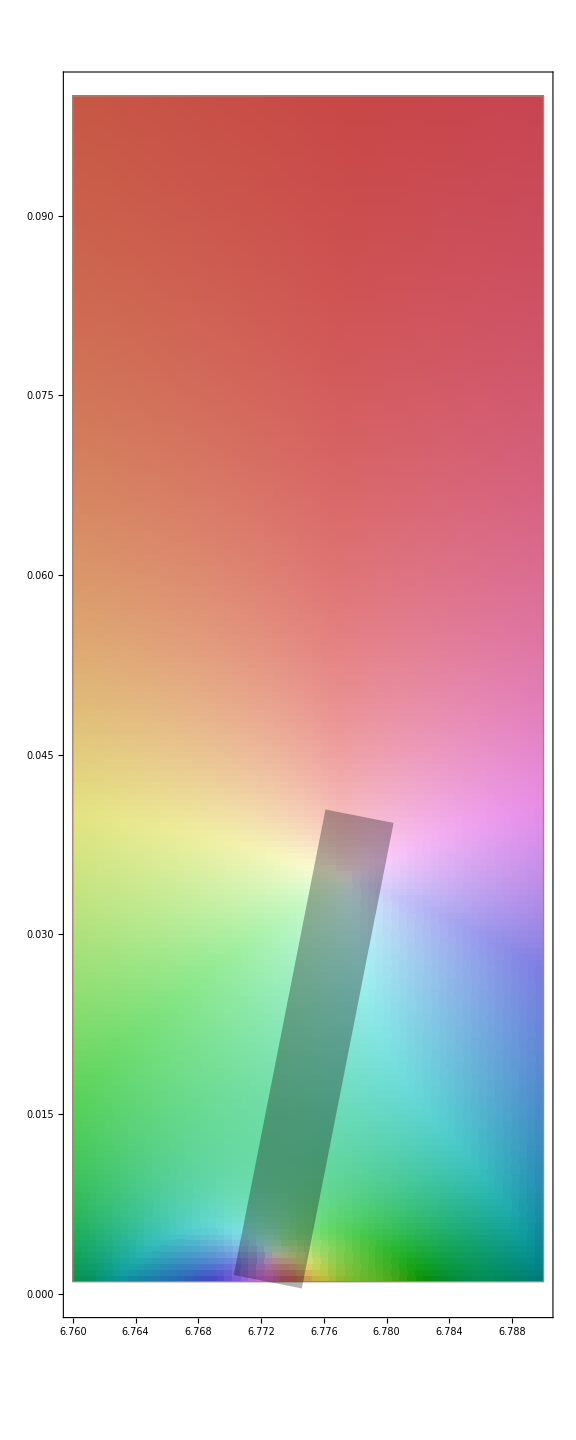

```mathematica
Row[{Module[{p1={1.4132,0.001},p2={1.4132,0.04}},Show[ParametricPlot[{x,y},{x,1.398,1.428},{y,0.001,0.1},
ColorFunction->Function[{x,y},Module[
{v=cFN[1000,x+I y]},
Hue[
Arg[v]/(2Pi),
Sqrt[Sin[2 Pi(LogisticSigmoid[0.5Abs[v]]-0.5)]],
1-1/(1+1/(0.5Abs[v]))
]
]],Axes->None,ColorFunctionScaling->False,PlotPoints->{60,200},
PlotRangePadding->0,ImageSize->Large],Graphics[{GrayLevel[0,0.3],Thickness[0.1],Line[{p1,p2}]}]]],Spacer[120],Module[{p1={6.7727573,0.00320243},p2={6.77750387,0.0347529}},Show[ParametricPlot[{x,y},{x,6.76,6.79},{y,0.001,0.1},
ColorFunction->Function[{x,y},Module[
{v=cFN[1000,x+I y]},
Hue[
Arg[v]/(2Pi),
Sqrt[Sin[2 Pi(LogisticSigmoid[0.5Abs[v]]-0.5)]],
1-1/(1+1/(0.5Abs[v]))
]
]],Axes->None,ColorFunctionScaling->False,PlotPoints->{60,200},
PlotRangePadding->0,ImageSize->Large],Graphics[{GrayLevel[0,0.3],Thickness[0.1],Line[{1.07p1-0.07p2,1.162p2-0.162p1}]}]]]}]
```

Along the highlighted segments:

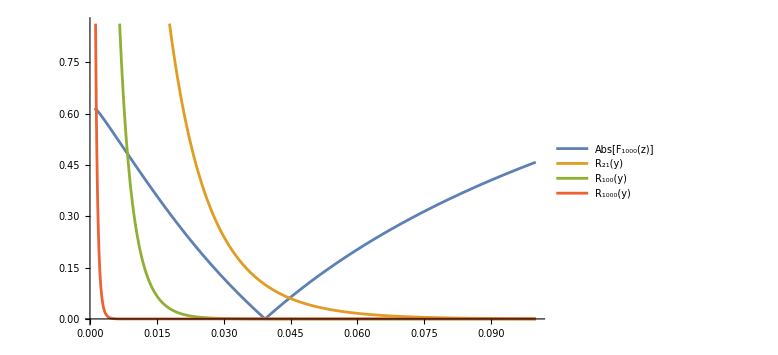
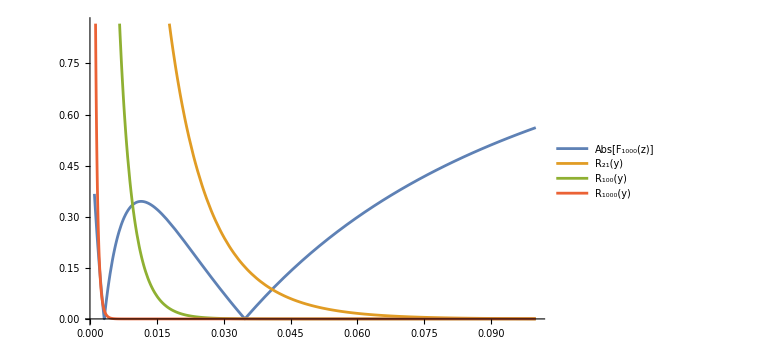

```mathematica
Column[{Plot[{Abs[cFN[1000,1.4132+I y]],cRN[21,y],cRN[100,y],cRN[1000,y]},{y,0.001,0.1},ImageSize->Large,PlotLegends->{,,,}],
Spacer[{10,60}],
Module[{p1={6.7727573,0.00320243},p2={6.77750387,0.0347529},a,b},
a=(p2[[1]]-p1[[1]])/(p2[[2]]-p1[[2]]);
b=p1[[1]]-a p1[[2]];
Plot[{Abs[cFN[1000,a y+b+I y]],cRN[21,y],cRN[100,y],cRN[1000,y]},{y,0.001,0.1},ImageSize->Large,PlotLegends->{,,,}]]}]
```

➔

## Why do zeros have copies?

Consider the structure of:

,      ,  .

Each summand is periodic with a different period.

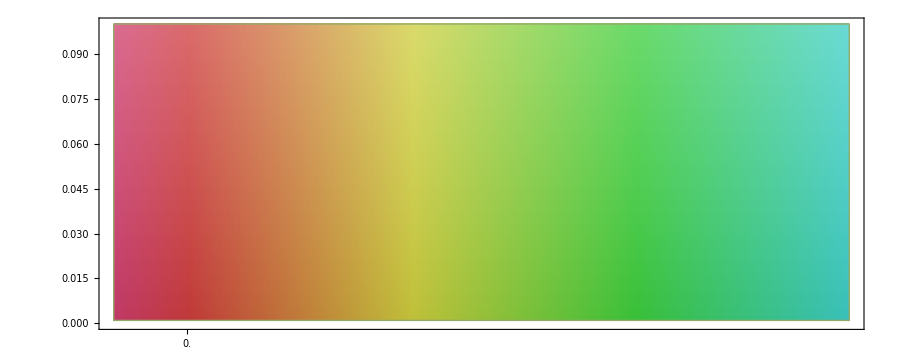
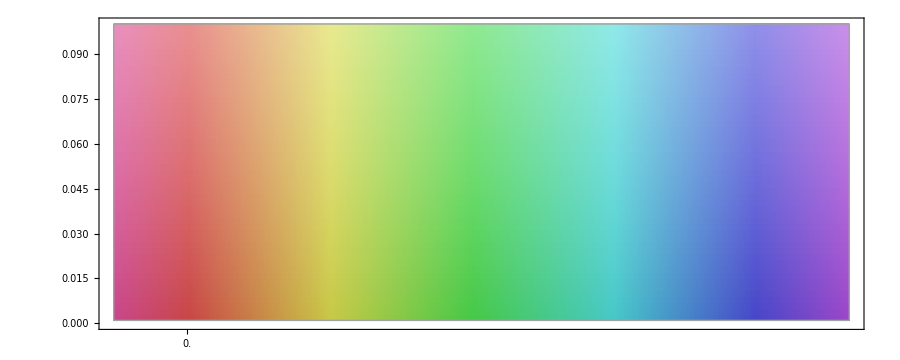
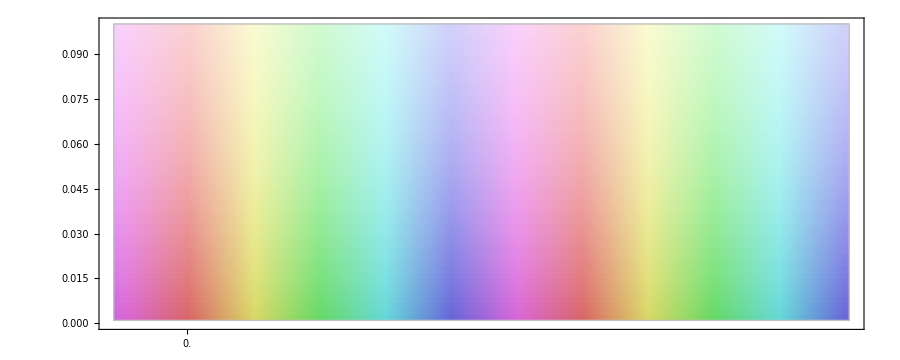
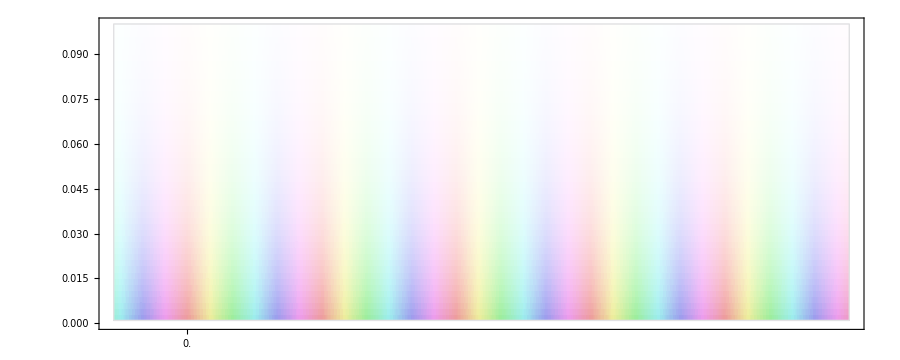
-Graphics-n = 1
-Graphics-n = 2
-Graphics-n = 5
-Graphics-n = 21

```mathematica
Column[Table[Row[{ParametricPlot[{x,y},{x,-0.05,0.45},{y,0.001,0.1},
ColorFunction->Function[{x,y},Module[
{v=rho[0]Exp[I(gamma[n]-gamma[0])(x+I y)]/rho[n]},
Hue[
Arg[v]/(2Pi),
Sqrt[Sin[2 Pi(LogisticSigmoid[0.5Abs[v]]-0.5)]],
1-1/(1+1/(0.5Abs[v]))
]
]],Axes->None,FrameTicks->{{Automatic,Automatic},{Table[0.1k,{k,0,70}],None}},ColorFunctionScaling->False,PlotPoints->{500,50},
ImageSize->900,PlotRangePadding->0],Spacer[40],Style["n = "<>ToString[n],"Text"]}],{n,{1,2,5,21}}]]
```

Find a zero of the partial sum

Move horizontally by

such that the alignment of phases is almost the same

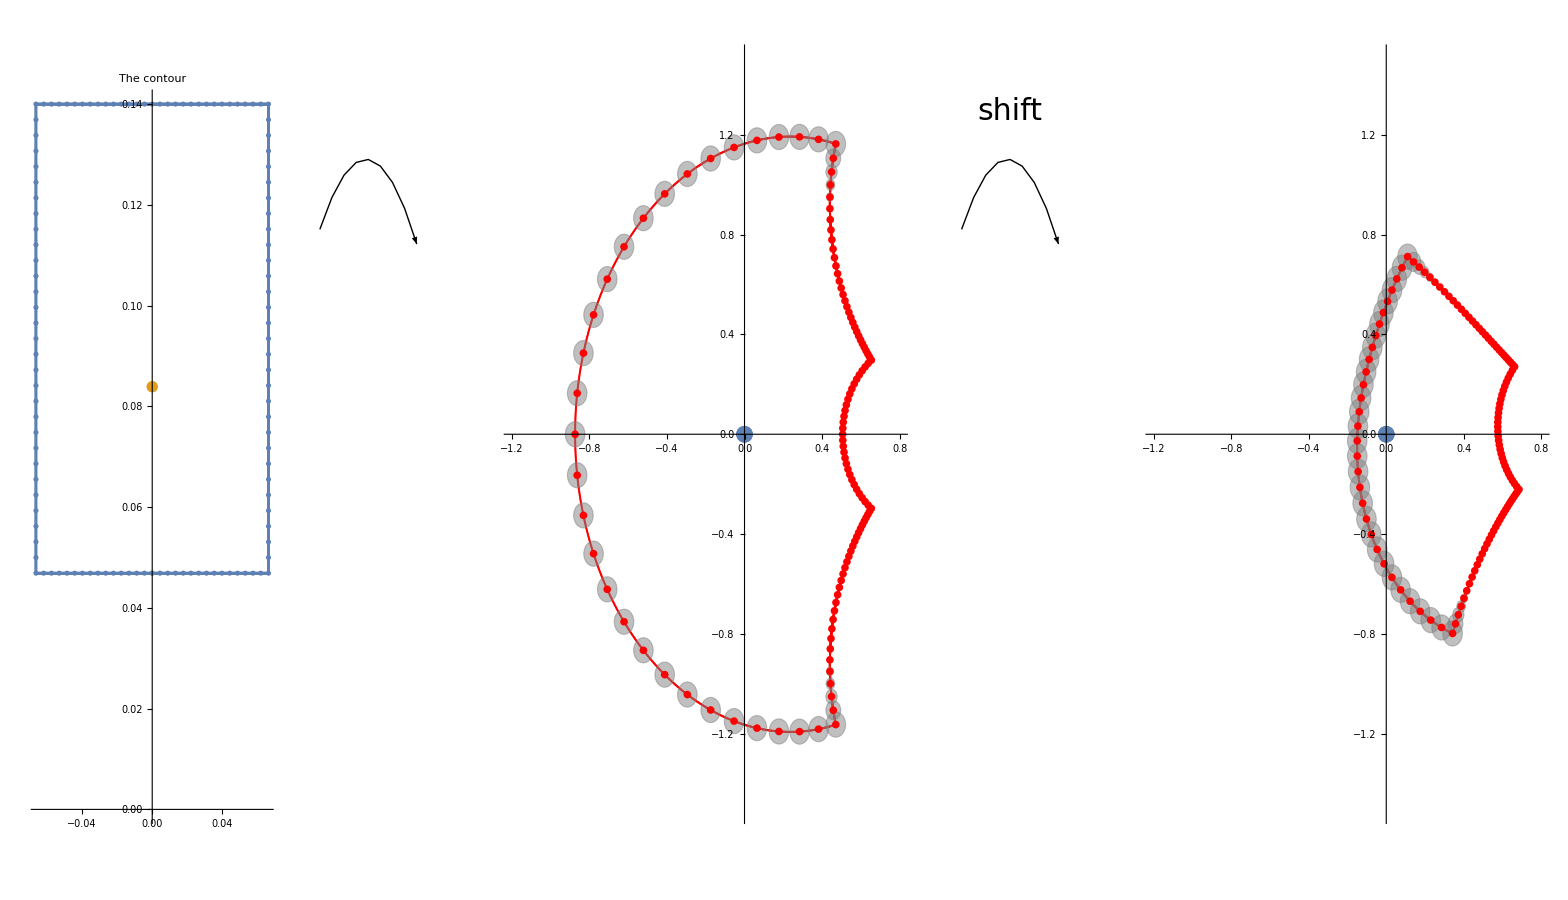

```mathematica
Pane[GraphicsRow[{
Show[
ComplexListPlot[{z1,{0.0839 I}},AspectRatio->1,PlotLabel->Style["The contour ",40],PlotStyle->{Automatic,PointSize[0.02]}],
ComplexListPlot[z1Sparse,AspectRatio->1]],
Graphics[{Thick,Arrowheads[.15],Arrow[BezierCurve[{{0,1},{1,2},{2,0.9}}]]},ImageSize->{150,300},PlotRange->{{0,2},{-3,2}}],
Show[
ComplexListPlot[{0},AspectRatio->1.5,PlotRange->{{-1.2,0.8},{-1.5,1.5}},PlotStyle->{PointSize[0.02]},ImagePadding->{{10,10},{15,15}},ImageSize->600,PlotLabel->Style["",40]],
ComplexListPlot[values,AspectRatio->1,PlotStyle->{Red,PointSize[0.0025]}],
Graphics[Join[{Gray,Opacity[0.5],EdgeForm[Thin]},Table[Disk[{Re[valuesSparse[[j]]],Im[valuesSparse[[j]]]},cRN[cN,Im[z1Sparse[[j]]]]],{j,1,mSparse}]]],
ComplexListPlot[valuesSparse,AspectRatio->1,PlotStyle->Red]],
Graphics[{Thick,Arrowheads[.15],Arrow[BezierCurve[{{0,1},{1,2},{2,0.9}}]],Text[Style["shift",30],{1,1.8}]},ImageSize->{150,300},PlotRange->{{0,2},{-3,2}}],
Module[{tau=633.51412-833.3473548418},
valuesShifted=Table[N[cFNeta[z1[[j]]+tau],10],{j,1,m}];
valuesShiftedSparse=Table[N[cFNeta[z1Sparse[[j]]+tau],10],{j,1,mSparse}];
Show[
ComplexListPlot[{0},AspectRatio->1.5,PlotRange->{{-1.2,0.8},{-1.5,1.5}},PlotStyle->{PointSize[0.02]},ImagePadding->{{10,10},{15,15}},ImageSize->600,PlotLabel->Style["",40]],
ComplexListPlot[valuesShifted,AspectRatio->1,PlotStyle->{Red,PointSize[0.0025]}],
Graphics[Join[{Gray,Opacity[0.5],EdgeForm[Thin]},Table[Disk[{Re[valuesShiftedSparse[[j]]],Im[valuesShiftedSparse[[j]]]},cRN[cN,Im[z1Sparse[[j]]]]],{j,1,mSparse}]]],
ComplexListPlot[valuesShiftedSparse,AspectRatio->1,PlotStyle->Red]]
]
},ImageSize->{2000,900}],
ImageSize->Full,Scrollbars->{True, False}
]
```

Shift:

by some ,

make sure all the 21 terms are in almost the same phase!

you get almost the same behaviour around the contour,

by the argument principle there is a zero inside the shifted contour.

What makes  admissible?

it is enough that

                                     

is small for n=1,...,21,

i.e.  maps into some sub-cube of the 21-dimensional unit cube

Finally:

estimate how often will all the 21 phases be sufficiently close to the initial position,

arrive at the density of zeros.

➔

## Key difference 1: Criterion for admissible τ

## New sufficient condition

Normalized -function

,      ,  .

```mathematica
Row[{
Manipulate[
Module[{selected=1+Mod[Floor[mSparse*Piecewise[{{slider/2,slider<0.3},{(1+slider)/2,slider>0.7}},1.75 slider-0.375]],mSparse],v,v1},
v={Re[valuesSparse[[selected]]],Im[valuesSparse[[selected]]]};
v1=(-1+rSparse[[selected]]/Norm[v])v;
Show[
ComplexListPlot[{0},AspectRatio->1.5,PlotRange->{{-1.2,0.8},{-1.5,1.5}},PlotStyle->{PointSize[0.01]},ImagePadding->{{10,10},{15,15}},ImageSize->600,PlotLabel->Style["Where can this value move to?",40]],
ComplexListPlot[values,AspectRatio->1,PlotStyle->{Red,PointSize[0.0025]}],
Graphics[{
Gray,Opacity[0.5],EdgeForm[Thin],
Disk[{Re[valuesSparse[[selected]]],Im[valuesSparse[[selected]]]},rSparse[[selected]]],
Black,
Arrow[{v,v+v1}],
InfiniteLine[v+v1,{v1[[2]],-v1[[1]]}],
Opacity[0.1],
HalfPlane[v+v1,{v1[[2]],-v1[[1]]},v],
Opacity[0.25],EdgeForm[Dashed],
Circle[{0,0},rSparse[[selected]]]
}],
ComplexListPlot[valuesSparse,AspectRatio->1,PlotStyle->Red]]
],
{{slider,0.97,"Selected point"},0,1}
],Spacer[20],
Column[{Style["For each point on the","Text"],Style["contour we prescribe","Text"],Style["a half-plane of allowed","Text"],Style["values.","Text"],Spacer[{1,100}],Style["These half-planes","Text"],Style["make a full circle.","Text"]}]
}]
```

For each point on the
contour we prescribe
a half-plane of allowed
values.

These half-planes
make a full circle.

Part::pkspec1: The expression 1 + Mod[Floor[0.989 mSparse], mSparse]
     cannot be used as a part specification.

General::stop: Further output of Part::pkspec1
     will be suppressed during this calculation.

ComplexListPlot::ldata: values is not a valid dataset or list of datasets.

ComplexListPlot::ldata: 
   valuesSparse is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in 
    Show[-Graphics-, ComplexListPlot[values, AspectRatio -> 1, 
      PlotStyle -> {RGBColor[1, 0, 0], PointSize[0.0025]}], -Graphics-, 
     ComplexListPlot[valuesSparse, AspectRatio -> 1, 
      PlotStyle -> RGBColor[1, 0, 0]]].

```mathematica
Row[{
Manipulate[
Module[{selected=1+Mod[Floor[mSparse*Piecewise[{{slider/2,slider<0.3},{(1+slider)/2,slider>0.7}},1.75 slider-0.375]],mSparse],v,v1},
v={Re[valuesSparse[[selected]]],Im[valuesSparse[[selected]]]};
v1={Cos[alphaSparse[[selected]]],Sin[alphaSparse[[selected]]]};
v1=-(v . v1-rSparse[[selected]])v1;
Show[
ComplexListPlot[{0},AspectRatio->1.5,PlotRange->{{-1.2,0.8},{-1.5,1.5}},PlotStyle->{PointSize[0.01]},ImagePadding->{{10,10},{15,15}},ImageSize->600,PlotLabel->Style["Where can this value move to?",40]],
ComplexListPlot[values,AspectRatio->1,PlotStyle->{Red,PointSize[0.0025]}],
Graphics[{
Gray,Opacity[0.5],EdgeForm[Thin],
Disk[{Re[valuesSparse[[selected]]],Im[valuesSparse[[selected]]]},rSparse[[selected]]],
Black,
Arrow[{v,v+v1}],
InfiniteLine[v+v1,{v1[[2]],-v1[[1]]}],
Opacity[0.1],
HalfPlane[v+v1,{v1[[2]],-v1[[1]]},v],
Opacity[0.25],EdgeForm[Dashed],
Circle[{0,0},rSparse[[selected]]]
}],
ComplexListPlot[valuesSparse,AspectRatio->1,PlotStyle->Red]]
],
{{slider,0.97,"Selected point"},0,1}
],Spacer[20],
Column[{Style["There is some flexibility","Text"],Style["in choosing the direction","Text"],Style["of allowed half–planes.","Text"],Spacer[{1,100}],Style["Their movement need not","Text"],Style["even be continuous!","Text"]}]
}]
```

There is some flexibility
in choosing the direction
of allowed half–planes.

Their movement need not
even be continuous!

Part::pkspec1: The expression 1 + Mod[Floor[0.985 mSparse], mSparse]
     cannot be used as a part specification.

General::stop: Further output of Part::pkspec1
     will be suppressed during this calculation.

ComplexListPlot::ldata: values is not a valid dataset or list of datasets.

ComplexListPlot::ldata: 
   valuesSparse is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in 
    Show[-Graphics-, ComplexListPlot[values, AspectRatio -> 1, 
      PlotStyle -> {RGBColor[1, 0, 0], PointSize[0.0025]}], -Graphics-, 
     ComplexListPlot[valuesSparse, AspectRatio -> 1, 
      PlotStyle -> RGBColor[1, 0, 0]]].

Part::pkspec1: The expression 1 + Mod[Floor[0.985 mSparse], mSparse]
     cannot be used as a part specification.

General::stop: Further output of Part::pkspec1
     will be suppressed during this calculation.

ComplexListPlot::ldata: values is not a valid dataset or list of datasets.

ComplexListPlot::ldata: 
   valuesSparse is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in 
    Show[-Graphics-, ComplexListPlot[values, AspectRatio -> 1, 
      PlotStyle -> {RGBColor[1, 0, 0], PointSize[0.0025]}], -Graphics-, 
     ComplexListPlot[valuesSparse, AspectRatio -> 1, 
      PlotStyle -> RGBColor[1, 0, 0]]].

The condition

{half-plane}

translates to a trigonometric inequality on

We replace

with an upper bound,

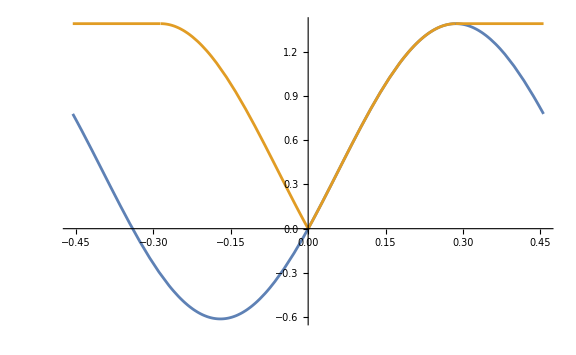

```mathematica
Module[
{n=1,j=500},
Plot[{(Cos[phiPrime[[n]][[j]]]-Cos[(gamma[n]-gamma[0])x+phiPrime[[n]][[j]]]),v[phiPrime[[n]][[j]],(gamma[n]-gamma[0])Abs[x]]},{x,-pi/(gamma[n]-gamma[0]),pi/(gamma[n]-gamma[0])},ImageSize->Large,PlotLegends->{"",""}]
]
```

and arrive at the normalized form (divided by RHS):

This has to hold for the entire contour, so we compute  of each summand over  and get the sufficient condition:

“Weights” or “penalty functions”:

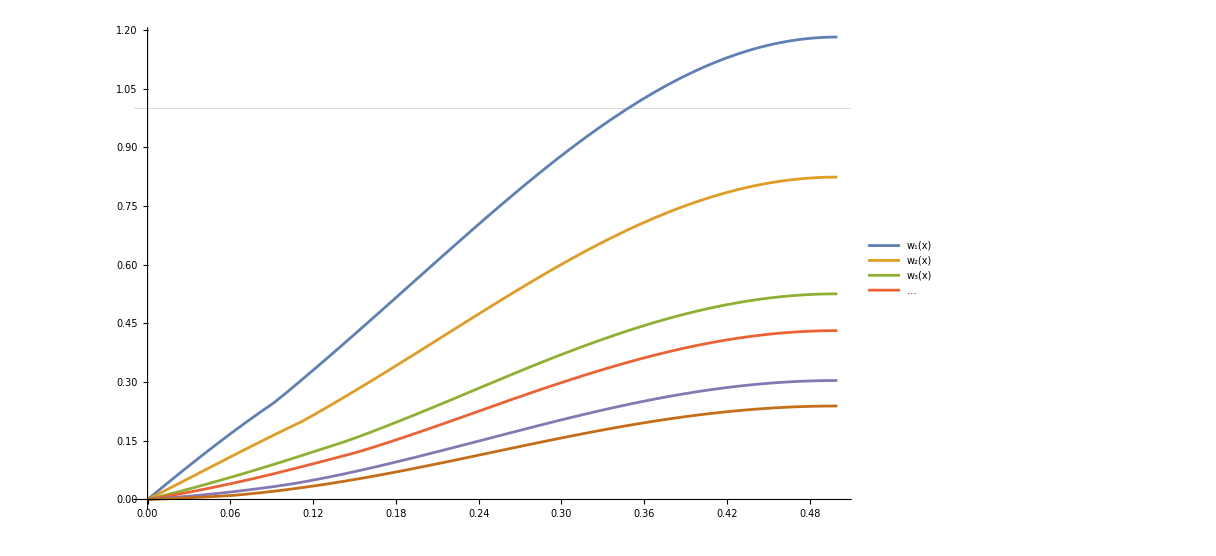

```mathematica
Plot[{w[1,x],w[2,x],w[3,x],w[4,x],w[5,x],w[6,x]},{x,0,0.5},PlotLegends->{,,,},GridLines->{{},{1}},ImageSize->900]
```

The “solution set” in 21-dimensional space (mod 1).
Denote it .

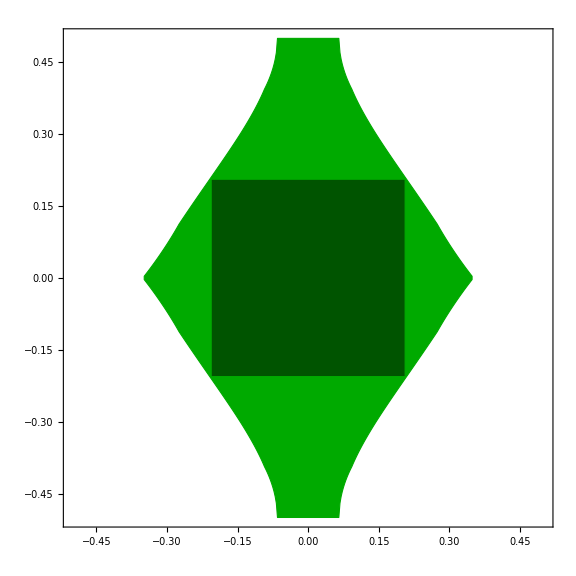
-Graphics-The set of admissible s maps to
a subset of .

By bounding the sum of penalty
functions, instead of each norm
individually, we can use all of ,
not a hypercube inscribed in .

```mathematica
Row[{
Show[
ComplexListPlot[{},PlotRange->{{-0.5,0.5},{-0.5,0.5}},Frame->True,Axes->False],
Graphics[{
Darker[Green],EdgeForm[Thick],Polygon[Join[
Table[{x[[1]][[j]],x[[2]][[ll+1-j]]},{j,ll}],
Table[{x[[1]][[ll+1-j]],-x[[2]][[j]]},{j,ll}],
Table[{-x[[1]][[j]],-x[[2]][[ll+1-j]]},{j,ll}],
Table[{-x[[1]][[ll+1-j]],x[[2]][[j]]},{j,ll}]
]],
Black,Opacity[0.5],Rectangle[{-0.206,-0.206},{0.206,0.206}]
}],ImageSize->Large
],
Spacer[20],
Column[{Style["The set of admissible s maps to","Text"],Style["a subset of .","Text"],Spacer[{1,20}],Style["By bounding the sum of penalty","Text"],Style["functions, instead of each norm","Text"],Style["individually, we can use all of ,","Text"],Style["not a hypercube inscribed in .","Text"]}]
}]
```

Result: , for N = 8.

➔

## Key difference 2: The tiling method

## What is the density of admissible s?

Every  maps to a point

in -dimensional space. The mapping

is linear. The mapping

+ ℤ

is additive.

### Classical problem in Diophantine approximation

Given , estimate the density of admissible s, i.e. such that

ℤ

```mathematica
mod1[x_]:=x-Floor[x+0.5];
Row[{
Manipulate[
Show[
ComplexListPlot[{},PlotRange->{{-0.5,0.5},{-0.5,0.5}},Frame->True,Axes->False],
Graphics[
Join[{
Darker[Green],EdgeForm[Thick],Polygon[Join[
Table[{x[[1]][[j]],x[[2]][[ll+1-j]]},{j,ll}],
Table[{x[[1]][[ll+1-j]],-x[[2]][[j]]},{j,ll}],
Table[{-x[[1]][[j]],-x[[2]][[ll+1-j]]},{j,ll}],
Table[{-x[[1]][[ll+1-j]],x[[2]][[j]]},{j,ll}]
]],
Black,Opacity[0.2],EdgeForm[]
},
{Union[Table[Disk[{mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]},0.01],{tau,0,slider,0.005}]]}
]],ImageSize->Large
],
{{slider,0.06,"max τ"},0,10,ImageSize->550}
],
Spacer[20],
Column[{Style["Conjecture: ","Subsubsection"],Style["Density equals .","Text"],
Spacer[{1,20}],Style["True, if  linearly independent","Text"],
Style["over ℚ (as conjectured by","Text"],Style["Aurel Wintner, 1935).","Text"],
Spacer[{1,20}],
Style["→ density of zeros ","Text"],Style["( is the width of the contour)","Text"]}]
}]
```

Conjecture: 
Density equals .

True, if  linearly independent
over ℚ (as conjectured by
Aurel Wintner, 1935).

→ density of zeros 
( is the width of the contour)

### Classical estimate

```mathematica
pl=ComplexListPlot[{},PlotRange->{{-0.5,0.5},{-0.5,0.5}},Frame->True,Axes->False];
gr=Graphics[{
Darker[Green],EdgeForm[Thick],Polygon[Join[
Table[{x[[1]][[j]],x[[2]][[ll+1-j]]},{j,ll}],
Table[{x[[1]][[ll+1-j]],-x[[2]][[j]]},{j,ll}],
Table[{-x[[1]][[j]],-x[[2]][[ll+1-j]]},{j,ll}],
Table[{-x[[1]][[ll+1-j]],x[[2]][[j]]},{j,ll}]
]]
}
];
pointsB=0.5{{0.345,0},{0,0.515},{-0.345,0},{0,-0.515}};
shiftedB=Polygon[Transpose[Transpose[pointsB]+{-0.3,0.2}]];
tau0=0.595;
val0={mod1[(gamma[1]-gamma[0])tau0/(2 pi)],mod1[(gamma[2]-gamma[0])tau0/(2 pi)]};
reshiftedB=Polygon[Transpose[Transpose[pointsB]+{-0.3,0.2}-val0]];
TabView[Table[Pane[item[[1]],ImageSize->165,BaseStyle->"NaturalLanguageInput"]->Deploy[item[[2]]],{item,{
{"1) Choose B",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.15],EdgeForm[Thick],
Polygon[pointsB]
}],ImageSize->Large
],
Spacer[20],
Column[{Pane["Choose a symmetric, convex set B⊂A…",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"… such that",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.45],EdgeForm[Thick],
Polygon[2pointsB],
Darker[Yellow,0.15],EdgeForm[Thick],
Polygon[pointsB]
}],ImageSize->Large
],
Spacer[20],
Column[{Pane["…such that B-B=2B⊂A",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"2) Shifted B ",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.15],EdgeForm[Thick],
shiftedB,
Black,Opacity[0.2],EdgeForm[],
Union[Table[
With[{disk=Disk[{mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]},0.01]},
If[RegionWithin[shiftedB,disk],disk]],
{tau,0,10,0.005}]]
}],ImageSize->Large
],
Spacer[20],
Column[{Pane["By the mean value theorem:",ImageSize->550,BaseStyle->"Subsubsection"],Pane["There is a shifted copy of B that gets many of the .",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"3) Set τ_0",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.15],EdgeForm[Thick],
shiftedB,
Black,Opacity[0.2],EdgeForm[],
Union[Table[
With[{disk=Disk[{mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]},0.01]},
If[RegionWithin[shiftedB,disk],disk]],
{tau,0,10,0.005}]],
Darker[Red],Opacity[1],EdgeForm[],
Disk[{mod1[(gamma[1]-gamma[0])tau0/(2 pi)],mod1[(gamma[2]-gamma[0])tau0/(2 pi)]},0.012]
}],ImageSize->Large
],
Spacer[20],
Column[{Pane["Let  be the first one.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"4) Shift …",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.15],EdgeForm[Thick],
shiftedB,
Black,Opacity[0.2],EdgeForm[],
Union[Table[
With[{disk=Disk[{mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]},0.01]},
If[RegionWithin[shiftedB,disk],disk]],
{tau,0,10,0.005}]],
Darker[Red],Opacity[1],EdgeForm[],
Disk[val0,0.012],
Thickness[0.008],
Arrow[{val0,{0,0}}]
}],ImageSize->Large
],
Spacer[20],
Column[{Pane["Remember, that the mapping is additive?",ImageSize->550,BaseStyle->"Text"],
Spacer[{1,20}],
Pane["So we can subtract the value at  from all the values we have found!",ImageSize->550,BaseStyle->"Text"],
}]
},ImageSize->Full]
},
{"… back to A",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.45],EdgeForm[Thick],
Polygon[2pointsB],
Darker[Yellow,0.15],EdgeForm[Thick],
reshiftedB,
Black,Opacity[0.2],EdgeForm[],
Union[Table[
With[{disk=Disk[{mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]}-val0,0.01]},
If[RegionWithin[reshiftedB,disk],disk]],
{tau,0,10,0.005}]],
Darker[Red],Opacity[1],EdgeForm[],
Disk[{0,0},0.012]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["The differences will be in B-B=2B⊂A.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"5) Result",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.15],EdgeForm[Thick],
reshiftedB,
Black,Opacity[0.2],EdgeForm[],
Union[Table[
With[{disk=Disk[{mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]}-val0,0.01]},
If[RegionWithin[reshiftedB,disk],disk]],
{tau,0,10,0.005}]],
Darker[Red],Opacity[1],EdgeForm[],
Disk[{0,0},0.012]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["The differences will be in B-B=2B⊂A.",ImageSize->550,BaseStyle->"Text"],
Spacer[{1,20}],
Pane["Result:",ImageSize->550,BaseStyle->"Subsubsection"],
Pane["Density ≥ vol(B).",ImageSize->550,BaseStyle->"Text"],
Spacer[{1,20}],
Pane["Unfortunately, vol(B) ≤ vol(A).",ImageSize->550,BaseStyle->"Text"],
Pane["The number of points in shifted  is correct, but we do not know where they are in .",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
}
}}],ControlPlacement->Left]
```

1234567

### The tiling method

```mathematica
pl=ComplexListPlot[{},PlotRange->{{-0.5,0.5},{-0.5,0.5}},Frame->True,Axes->False];
regionA=Polygon[Join[
Table[{x[[1]][[j]],x[[2]][[ll+1-j]]},{j,ll}],
Table[{x[[1]][[ll+1-j]],-x[[2]][[j]]},{j,ll}],
Table[{-x[[1]][[j]],-x[[2]][[ll+1-j]]},{j,ll}],
Table[{-x[[1]][[ll+1-j]],x[[2]][[j]]},{j,ll}]
]];
gr=Graphics[{
Darker[Green],EdgeForm[Thick],regionA
}
];
latticeColor=Darker[RGBColor[1,0.14,0.0],0.2];
latticeColor=Blend[{Darker[Brown],Darker[Red]},0.5];
tau1=4.625;
tau2=6.4;
val1={mod1[(gamma[1]-gamma[0])tau1/(2 pi)],mod1[(gamma[2]-gamma[0])tau1/(2 pi)]};
val2={mod1[(gamma[1]-gamma[0])tau2/(2 pi)],mod1[(gamma[2]-gamma[0])tau2/(2 pi)]};
pointsP=0.5{-val1-val2,val1-val2,val1+val2,-val1+val2};
val0=-0.25val1-0.4val2;
val00=val0+{mod1[(gamma[1]-gamma[0])10.995/(2 pi)],mod1[(gamma[2]-gamma[0])10.995/(2 pi)]};
val01=val0+{mod1[(gamma[1]-gamma[0])17.37/(2 pi)],mod1[(gamma[2]-gamma[0])17.37/(2 pi)]};
shiftedP=Polygon[Transpose[Transpose[pointsP]-val0]];
inP=Select[Table[tau,{tau,tau1,15+tau1,0.005}],RegionWithin[shiftedP,Disk[{mod1[(gamma[1]-gamma[0])#/(2 pi)],mod1[(gamma[2]-gamma[0])#/(2 pi)]},0.005]]&];
inA=Select[Flatten[Table[Table[
With[{pt=k1 val1+k2 val2},
If[RegionWithin[regionA,Polygon[Transpose[Transpose[2pointsP]+pt]]],
{k1,k2},{}
]],
{k1,-3,3}],{k2,-5,5}],1],Length[#]>0&];
TabView[Table[Pane[item[[1]],ImageSize->185,BaseStyle->"NaturalLanguageInput"]->Deploy[item[[2]]],{item,{
{"1) Find a…",
Row[{
Show[
pl,gr,
Graphics[{
Black,Opacity[0.2],EdgeForm[],
Union[Table[
Disk[{mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]},0.01],
{tau,0,10,0.005}]],
latticeColor,Opacity[1],EdgeForm[],
Disk[val1,0.012],
Disk[val2,0.012]
}],ImageSize->Large
],
Spacer[20],
Column[{Pane["Choose  reachable points…",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"… basis of ℝ^N",
Row[{
Show[
pl,gr,
Graphics[{
Black,Opacity[0.2],EdgeForm[],
Union[Table[
Disk[{mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]},0.01],
{tau,0,10,0.005}]],
latticeColor,Opacity[1],EdgeForm[],
Disk[val1,0.012],
Disk[val2,0.012],
Thickness[0.008],
Arrow[{{0,0},val1}],
Arrow[{{0,0},val2}]
}],ImageSize->Large
],
Spacer[20],
Column[{Pane["…that make a basis of ℝ^N.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"2) Lattice…",
Row[{
Show[
pl,gr,
Graphics[{
latticeColor,Opacity[1],EdgeForm[],
Union[Table[Table[
With[{pt=k1 val1+k2 val2},
Disk[pt,0.01]],
{k1,-8,8}],{k2,-7,7}]]
}],ImageSize->Large
],
Spacer[20],
Column[{Pane["They span a lattice of reachable points…",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"   …inside ",
Row[{
Show[
pl,gr,
Graphics[{
latticeColor,Opacity[1],EdgeForm[],
Union[Table[
With[{pt=k[[1]] val1+k[[2]] val2},
Disk[pt,0.01]
],{k,inA}]]
}],ImageSize->Large
],
Spacer[20],
Column[{Pane["…from which we select those deep inside .",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"3) The tile…",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.15],EdgeForm[Thick],
Polygon[pointsP],
Black,Opacity[0.25],
Union[Table[Table[
With[{pt=k1 val1+k2 val2},
{Line[{pt,pt+val1}],Line[{pt,pt-val1}],Line[{pt,pt+val2}]}],
{k1,-8,8}],{k2,-7,7}]],
latticeColor,Opacity[1],EdgeForm[],
Union[Table[Table[
With[{pt=k1 val1+k2 val2},
Disk[pt,0.01]],
{k1,-8,8}],{k2,-7,7}]]
}],ImageSize->Large
],
Spacer[20],
Column[{Pane["Let  denote the fundamental parallelotope of our lattice.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"   …shifted",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.15],EdgeForm[Thick],
shiftedP,
Black,Opacity[0.2],EdgeForm[],
Union[Table[
With[{pt={mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]}},
Disk[pt,0.01]],
{tau,inP}]],
latticeColor,Opacity[1],EdgeForm[],
Disk[{0,0},0.012]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["Apply the *classical* argument to .",ImageSize->550,BaseStyle->"Text"],
Pane["Given a large ,",ImageSize->550,BaseStyle->"Text"],
Pane["you will have a shifted copy of  catching many of the .",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"4) The tiling",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.15],EdgeForm[Thick],
Union[Table[
With[{pt=k[[1]] val1+k[[2]] val2},
Polygon[Transpose[Transpose[pointsP]-val0+pt]]
],{k,inA}]],
Black,Opacity[0.2],EdgeForm[],
Union[Table[
With[{pt0=k[[1]] val1+k[[2]] val2},
Table[
With[{pt={mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]}},
Disk[pt0+pt,0.01]],
{tau,inP}]
],{k,inA}]],
Darker[latticeColor],Opacity[1],EdgeForm[],
Union[Table[
With[{pt=k[[1]] val1+k[[2]] val2},
Disk[pt,0.01]
],{k,inA}]],
latticeColor,Opacity[1],EdgeForm[],
Disk[{0,0},0.012]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["Using additivity again:",ImageSize->550,BaseStyle->"Text"],
Spacer[{1,20}],
Pane["we shift the tile by lattice elements, getting more reachable points!",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"    (or tilings)",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.15],EdgeForm[Thick],
Union[Table[
With[{pt=k[[1]] val1+k[[2]] val2},
Polygon[Transpose[Transpose[pointsP]-val00+pt]]
],{k,inA}]],
Black,Opacity[0.2],EdgeForm[],
Union[Table[
With[{pt0=k[[1]] val1+k[[2]] val2},
Table[
With[{pt={mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]}},
Disk[pt0+pt+val0-val00,0.01]],
{tau,inP}]
],{k,inA}]],
Darker[latticeColor],Opacity[1],EdgeForm[],
Union[Table[
With[{pt=k[[1]] val1+k[[2]] val2},
Disk[pt,0.01]
],{k,inA}]],
latticeColor,Opacity[1],EdgeForm[],
Disk[{0,0},0.012]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["We still do not know where exactly the tile will be placed!",ImageSize->550,BaseStyle->"Text"],
Spacer[{1,20}],
Pane["But in any case the tiles will match their neighbours.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"    …",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.15],EdgeForm[Thick],
Union[Table[
With[{pt=k[[1]] val1+k[[2]] val2},
Polygon[Transpose[Transpose[pointsP]-val01+pt]]
],{k,inA}]],
Black,Opacity[0.2],EdgeForm[],
Union[Table[
With[{pt0=k[[1]] val1+k[[2]] val2},
Table[
With[{pt={mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]}},
Disk[pt0+pt+val0-val01,0.01]],
{tau,inP}]
],{k,inA}]],
Darker[latticeColor],Opacity[1],EdgeForm[],
Union[Table[
With[{pt=k[[1]] val1+k[[2]] val2},
Disk[pt,0.01]
],{k,inA}]],
latticeColor,Opacity[1],EdgeForm[],
Disk[{0,0},0.012]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["We still do not know where exactly the tile will be placed!",ImageSize->550,BaseStyle->"Text"],
Spacer[{1,20}],
Pane["But in any case the tiles will match their neighbours.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"5) Result",
Row[{
Show[
pl,gr,
Graphics[{
Darker[Yellow,0.15],EdgeForm[Thick],
Union[Table[
With[{pt=k[[1]] val1+k[[2]] val2},
Polygon[Transpose[Transpose[pointsP]-val01+pt]]
],{k,inA}]],
Black,Opacity[0.2],EdgeForm[],
Union[Table[
With[{pt0=k[[1]] val1+k[[2]] val2},
Table[
With[{pt={mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]}},
Disk[pt0+pt+val0-val01,0.01]],
{tau,inP}]
],{k,inA}]],
Darker[latticeColor],Opacity[1],EdgeForm[],
Union[Table[
With[{pt=k[[1]] val1+k[[2]] val2},
Disk[pt,0.01]
],{k,inA}]],
latticeColor,Opacity[1],EdgeForm[],
Disk[{0,0},0.012]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["Losses occur near the edges.",ImageSize->550,BaseStyle->"Text"],
Spacer[{1,20}],
Pane["If you make the basis really small, the difference between the density and vol(A) is beyond the reported decimal places.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
}
}}],ControlPlacement->Left]
```

12345678910

➔

## How to find a small basis of reachable vectors?

## What vectors are reachable?

Let  .

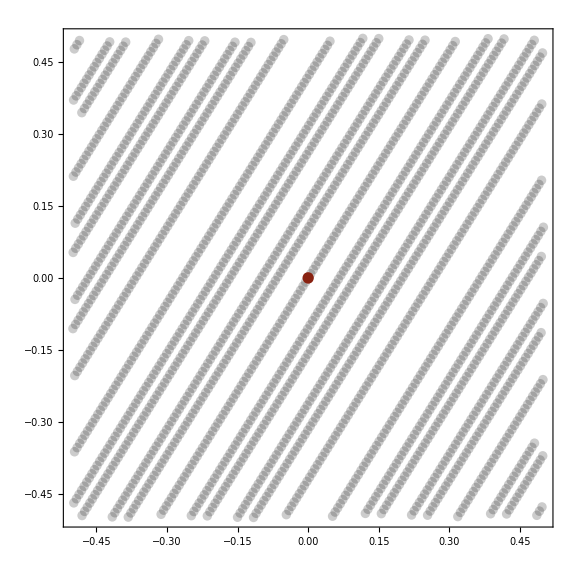
-Graphics-By definition, a reachable vector equals , t ∈ ℝ, mod 1

```mathematica
Row[{
Show[
pl,
Graphics[{
Black,Opacity[0.2],EdgeForm[],
Union[Table[
Disk[{mod1[(gamma[1]-gamma[0])tau/(2 pi)],mod1[(gamma[2]-gamma[0])tau/(2 pi)]},0.01],
{tau,-5,5,0.005}]],
latticeColor,Opacity[1],EdgeForm[],
Disk[{0,0},0.012]
}],ImageSize->Large
],
Spacer[20],
Column[{Pane["By definition, a reachable vector equals , t ∈ ℝ, mod 1",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
```

The set of reachable vectors equals

∪_(t∈ℝ) tθ + ℤ^N.

It means that we can use:

generators of ℤ^N,

,

all multiples tθ, t ∈ ℝ,

integer combinations of reachable vectors.

```mathematica
pl3=ComplexListPlot[{},PlotRange->{{-1.5,1.5},{-1.5,1.5}},Frame->True,Axes->False];
latticeColor=Blend[{Darker[Brown],Darker[Red]},0.5];
theta={gamma[1]-gamma[0],gamma[2]-gamma[0]};
e1={1,0};
e1p=e1-((e1 . theta)/(theta . theta))theta;
e2={0,1};
e2p=e2-((e2 . theta)/(theta . theta))theta;
theta3={gamma[1]-gamma[0],gamma[2]-gamma[0],gamma[3]-gamma[0]};
e31ort={1,0,0}-({1,0,0}.theta3)/(theta3.theta3)theta3;
e31ort/=Norm[e31ort];
e32ort={0,1,0}-({0,1,0}.theta3)/(theta3.theta3)theta3-({0,1,0}.e31ort)e31ort;
e32ort/=Norm[e32ort];
vis=Transpose[{e31ort,e32ort}];
latSize=3;
TabView[Table[Pane[item[[1]],ImageSize->185,BaseStyle->"NaturalLanguageInput"]->Deploy[item[[2]]],{item,{
{"1) Starting",
Row[{
Show[
pl3,
Graphics[{
Black,Opacity[0.3],Thickness[0.0015],
InfiniteLine[{0.5,0.5},e1],InfiniteLine[{-0.5,-0.5},e1],
InfiniteLine[{0.5,0.5},e2],InfiniteLine[{-0.5,-0.5},e2],
Black,Opacity[0.2],EdgeForm[],
Disk[e1,0.03],
Disk[e2,0.03],
Union[Table[
Disk[t theta,0.03],
{t,-0.15,0.15,0.004}]],
Black,Opacity[1],EdgeForm[],Thickness[0.003],
InfiniteLine[{0,0},theta],
Arrow[{{0,0},e1}],
Arrow[{{0,0},e2}],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["We can use:",ImageSize->550,BaseStyle->"Text"],
Pane["  • ,",ImageSize->550,BaseStyle->"Text"],
Pane["  • all multiples tθ, t ∈ ℝ.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"2) ϵθ",
Row[{
Show[
pl3,
Graphics[{
Black,Opacity[0.3],Thickness[0.0015],
InfiniteLine[{0.5,0.5},e1],InfiniteLine[{-0.5,-0.5},e1],
InfiniteLine[{0.5,0.5},e2],InfiniteLine[{-0.5,-0.5},e2],
Black,Opacity[0.2],EdgeForm[],
Disk[e1,0.03],
Disk[e2,0.03],
Union[Table[
Disk[t theta,0.03],
{t,-0.15,0.15,0.004}]],
Black,Opacity[1],EdgeForm[],Thickness[0.003],
InfiniteLine[{0,0},theta],
Arrow[{{0,0},e1}],
Arrow[{{0,0},e2}],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[0.016 theta,0.036],
Darker[Red],
Arrow[{{0,0},0.016 theta}]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["What we do:",ImageSize->550,BaseStyle->"Text"],
Pane["  • select ϵθ as the first basis",ImageSize->550,BaseStyle->"Text"],
Pane["     vector (ϵ arbitrarily small)",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"3) Projection",
Row[{
Show[
pl3,
Graphics[{
Black,Opacity[0.3],Thickness[0.0015],
InfiniteLine[{0.5,0.5},e1],InfiniteLine[{-0.5,-0.5},e1],
InfiniteLine[{0.5,0.5},e2],InfiniteLine[{-0.5,-0.5},e2],
InfiniteLine[{0,0},{theta[[2]],-theta[[1]]}],
Black,Opacity[0.2],EdgeForm[],
Disk[e1,0.03],Disk[e1p,0.03],
Disk[e2,0.03],Disk[e2p,0.03],
Union[Table[
Disk[t theta,0.03],
{t,-0.15,0.15,0.004}]],
Black,Opacity[1],EdgeForm[],Thickness[0.003],
InfiniteLine[{0,0},theta],
Arrow[{{0,0},e1}],
Arrow[{{0,0},e2}],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[0.016 theta,0.036],
Darker[Red],
Arrow[{{0,0},0.016 theta}],
Dashed,Black,Opacity[1],Thickness[0.003],
Line[{e1,e1p}], Line[{e2,e2p}]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["What we do:",ImageSize->550,BaseStyle->"Text"],
Pane["  • select ϵθ as the first basis",ImageSize->550,BaseStyle->"Text"],
Pane["     vector (ϵ arbitrarily small)",ImageSize->550,BaseStyle->"Text"],
Pane["  • project all  onto the",ImageSize->550,BaseStyle->"Text"],
Pane["     orthogonal space of θ",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"     …",
Row[{
Show[
pl3,
Graphics[{
Black,Opacity[0.3],Thickness[0.0015],
InfiniteLine[{0.5,0.5},e1],InfiniteLine[{-0.5,-0.5},e1],
InfiniteLine[{0.5,0.5},e2],InfiniteLine[{-0.5,-0.5},e2],
InfiniteLine[{0,0},{theta[[2]],-theta[[1]]}],
Black,Opacity[0.2],EdgeForm[],
Disk[e1,0.03],
Disk[e2,0.03],
Union[Table[
Disk[t theta,0.03],
{t,-0.15,0.15,0.004}]],
Black,Opacity[1],EdgeForm[],Thickness[0.003],
InfiniteLine[{0,0},theta],
Arrow[{{0,0},e1}],
Arrow[{{0,0},e2}],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[0.016 theta,0.036],
Disk[e1p,0.036],Disk[e2p,0.036],
Darker[Red],
Arrow[{{0,0},0.016 theta}],
Arrow[{{0,0},e1p}],Arrow[{{0,0},e2p}],
Dashed,Black,Opacity[1],Thickness[0.003],
Line[{e1,e1p}], Line[{e2,e2p}]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["What we do:",ImageSize->550,BaseStyle->"Text"],
Pane["  • select ϵθ as the first basis",ImageSize->550,BaseStyle->"Text"],
Pane["     vector (ϵ arbitrarily small)",ImageSize->550,BaseStyle->"Text"],
Pane["  • project all  onto the",ImageSize->550,BaseStyle->"Text"],
Pane["     orthogonal space of θ",ImageSize->550,BaseStyle->"Text"],
Pane["  • obtain N vectors that span",ImageSize->550,BaseStyle->"Text"],
Pane["     N-1-dimensional subspace",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"4) Abundance",
Row[{
Show[
pl3,
Graphics[{
Black,Opacity[0.3],Thickness[0.0015],
InfiniteLine[{0.5,0.5},e1],InfiniteLine[{-0.5,-0.5},e1],
InfiniteLine[{0.5,0.5},e2],InfiniteLine[{-0.5,-0.5},e2],
InfiniteLine[{0,0},{theta[[2]],-theta[[1]]}],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[e1p,0.036],Disk[e2p,0.036],
Darker[Red],
Arrow[{{0,0},e1p}],Arrow[{{0,0},e2p}]
}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["Those N vectors are:",ImageSize->550,BaseStyle->"Text"],
Pane["  • linearly dependent over ℝ,",ImageSize->550,BaseStyle->"Text"],
Pane["  • possibly independent over ℚ.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"     …",
Row[{
Show[
Graphics[{
Black,Opacity[0.3],Thickness[0.0015],
Line[0.999{{-1.5,-1.5},{1.5,-1.5},{1.5,1.5},{-1.5,1.5},{-1.5,-1.5}}],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[{Norm[e1p],0},0.036],Disk[{-Norm[e2p],0},0.036],
Darker[Red],
Arrow[{{0,0},{Norm[e1p],0}}],Arrow[{{0,0},{-Norm[e2p],0}}],
},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["Those N vectors are:",ImageSize->550,BaseStyle->"Text"],
Pane["  • linearly dependent over ℝ,",ImageSize->550,BaseStyle->"Text"],
Pane["  • possibly independent over ℚ.",ImageSize->550,BaseStyle->"Text"],
Spacer[{1,20}],
Pane["For N = 2 they can be reduced easily.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"     …",
Row[{
latSize=1;
Show[
Graphics[{
Arrowheads[0.02],Black,Opacity[0.3],Thickness[0.0015],
Line[0.999{{-1.5,-1.5},{1.5,-1.5},{1.5,1.5},{-1.5,1.5},{-1.5,-1.5}}],
Union[Table[Table[Table[Arrow[{j vis[[1]]+k vis[[2]]+(i-1)vis[[3]],j vis[[1]]+k vis[[2]]+i vis[[3]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[2]]+k vis[[3]]+(i-1)vis[[1]],j vis[[2]]+k vis[[3]]+i vis[[1]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[3]]+k vis[[1]]+(i-1)vis[[2]],j vis[[3]]+k vis[[1]]+i vis[[2]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Arrowheads[Automatic],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[vis[[1]],0.036],Disk[vis[[2]],0.036],Disk[vis[[3]],0.036],
Darker[Red],
Arrow[{{0,0},vis[[1]]}],Arrow[{{0,0},vis[[2]]}],Arrow[{{0,0},vis[[3]]}]
},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["Those N vectors are:",ImageSize->550,BaseStyle->"Text"],
Pane["  • linearly dependent over ℝ,",ImageSize->550,BaseStyle->"Text"],
Pane["  • possibly independent over ℚ.",ImageSize->550,BaseStyle->"Text"],
Spacer[{1,20}],
Pane["For general N we have modified the LLL algorithm to reduce them.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"5) LLL",
Row[{
latSize=2;
Show[
Graphics[{
Arrowheads[0.02],Black,Opacity[0.3],Thickness[0.0015],
Line[0.999{{-1.5,-1.5},{1.5,-1.5},{1.5,1.5},{-1.5,1.5},{-1.5,-1.5}}],
Union[Table[Table[Table[Arrow[{j vis[[1]]+k vis[[2]]+(i-1)vis[[3]],j vis[[1]]+k vis[[2]]+i vis[[3]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[2]]+k vis[[3]]+(i-1)vis[[1]],j vis[[2]]+k vis[[3]]+i vis[[1]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[3]]+k vis[[1]]+(i-1)vis[[2]],j vis[[3]]+k vis[[1]]+i vis[[2]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Arrowheads[Automatic],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[vis[[1]],0.036],Disk[vis[[2]],0.036],Disk[vis[[3]],0.036],
Darker[Red],
Arrow[{{0,0},vis[[1]]}],Arrow[{{0,0},vis[[2]]}],Arrow[{{0,0},vis[[3]]}]
},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["LLL Algorithm changes:",ImageSize->550,BaseStyle->"Subsubsection"],
Pane["  • scope (dependent vectors)",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"     …",
Row[{
latSize=3;
Show[
Graphics[{
Arrowheads[0.02],Black,Opacity[0.3],Thickness[0.0015],
Line[0.999{{-1.5,-1.5},{1.5,-1.5},{1.5,1.5},{-1.5,1.5},{-1.5,-1.5}}],
Union[Table[Table[Table[Arrow[{j vis[[1]]+k vis[[2]]+(i-1)vis[[3]],j vis[[1]]+k vis[[2]]+i vis[[3]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[2]]+k vis[[3]]+(i-1)vis[[1]],j vis[[2]]+k vis[[3]]+i vis[[1]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[3]]+k vis[[1]]+(i-1)vis[[2]],j vis[[3]]+k vis[[1]]+i vis[[2]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Arrowheads[Automatic],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[vis[[1]],0.036],Disk[vis[[2]],0.036],Disk[vis[[3]],0.036],
Darker[Red],
Arrow[{{0,0},vis[[1]]}],Arrow[{{0,0},vis[[2]]}],Arrow[{{0,0},vis[[3]]}]
},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["LLL Algorithm changes:",ImageSize->550,BaseStyle->"Subsubsection"],
Pane["  • scope (dependent vectors),",ImageSize->550,BaseStyle->"Text"],
Pane["  • upper bound on coefficients",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"     …",
Row[{
latSize=4;
Show[
Graphics[{
Arrowheads[0.02],Black,Opacity[0.3],Thickness[0.0015],
Line[0.999{{-1.5,-1.5},{1.5,-1.5},{1.5,1.5},{-1.5,1.5},{-1.5,-1.5}}],
Union[Table[Table[Table[Arrow[{j vis[[1]]+k vis[[2]]+(i-1)vis[[3]],j vis[[1]]+k vis[[2]]+i vis[[3]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[2]]+k vis[[3]]+(i-1)vis[[1]],j vis[[2]]+k vis[[3]]+i vis[[1]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[3]]+k vis[[1]]+(i-1)vis[[2]],j vis[[3]]+k vis[[1]]+i vis[[2]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Arrowheads[Automatic],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[vis[[1]],0.036],Disk[vis[[2]],0.036],Disk[vis[[3]],0.036],
Darker[Red],
Arrow[{{0,0},vis[[1]]}],Arrow[{{0,0},vis[[2]]}],Arrow[{{0,0},vis[[3]]}]
},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["LLL Algorithm changes:",ImageSize->550,BaseStyle->"Subsubsection"],
Pane["  • scope (dependent vectors),",ImageSize->550,BaseStyle->"Text"],
Pane["  • upper bound on coefficients",ImageSize->550,BaseStyle->"Text"],
Pane["     (we used 10^300 for N=21)",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"     …",
Row[{
latSize=5;
Show[
Graphics[{
Arrowheads[0.02],Black,Opacity[0.3],Thickness[0.0015],
Line[0.999{{-1.5,-1.5},{1.5,-1.5},{1.5,1.5},{-1.5,1.5},{-1.5,-1.5}}],
Union[Table[Table[Table[Arrow[{j vis[[1]]+k vis[[2]]+(i-1)vis[[3]],j vis[[1]]+k vis[[2]]+i vis[[3]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[2]]+k vis[[3]]+(i-1)vis[[1]],j vis[[2]]+k vis[[3]]+i vis[[1]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[3]]+k vis[[1]]+(i-1)vis[[2]],j vis[[3]]+k vis[[1]]+i vis[[2]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Arrowheads[Automatic],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[vis[[1]],0.036],Disk[vis[[2]],0.036],Disk[vis[[3]],0.036],
Darker[Red],
Arrow[{{0,0},vis[[1]]}],Arrow[{{0,0},vis[[2]]}],Arrow[{{0,0},vis[[3]]}]
},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["LLL Algorithm changes:",ImageSize->550,BaseStyle->"Subsubsection"],
Pane["  • scope (dependent vectors),",ImageSize->550,BaseStyle->"Text"],
Pane["  • upper bound on coefficients",ImageSize->550,BaseStyle->"Text"],
Pane["     (we used 10^300 for N=21),",ImageSize->550,BaseStyle->"Text"],
Pane["  • δ=1/4 (for performance)",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"     …",
Row[{
latSize=6;
Show[
Graphics[{
Arrowheads[0.02],Black,Opacity[0.3],Thickness[0.0015],
Line[0.999{{-1.5,-1.5},{1.5,-1.5},{1.5,1.5},{-1.5,1.5},{-1.5,-1.5}}],
Union[Table[Table[Table[Arrow[{j vis[[1]]+k vis[[2]]+(i-1)vis[[3]],j vis[[1]]+k vis[[2]]+i vis[[3]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[2]]+k vis[[3]]+(i-1)vis[[1]],j vis[[2]]+k vis[[3]]+i vis[[1]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[3]]+k vis[[1]]+(i-1)vis[[2]],j vis[[3]]+k vis[[1]]+i vis[[2]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Arrowheads[Automatic],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[vis[[1]],0.036],Disk[vis[[2]],0.036],Disk[vis[[3]],0.036],
Darker[Red],
Arrow[{{0,0},vis[[1]]}],Arrow[{{0,0},vis[[2]]}],Arrow[{{0,0},vis[[3]]}]
},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["LLL Algorithm changes:",ImageSize->550,BaseStyle->"Subsubsection"],
Pane["  • scope (dependent vectors),",ImageSize->550,BaseStyle->"Text"],
Pane["  • upper bound on coefficients",ImageSize->550,BaseStyle->"Text"],
Pane["     (we used 10^300 for N=21),",ImageSize->550,BaseStyle->"Text"],
Pane["  • δ=1/4 (for performance),",ImageSize->550,BaseStyle->"Text"],
Pane["  • recomputing vectors from",ImageSize->550,BaseStyle->"Text"],
Pane["     coefficients",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"     …",
Row[{
latSize=8;
Show[
Graphics[{
Arrowheads[0.02],Black,Opacity[0.3],Thickness[0.0015],
Line[0.999{{-1.5,-1.5},{1.5,-1.5},{1.5,1.5},{-1.5,1.5},{-1.5,-1.5}}],
Union[Table[Table[Table[Arrow[{j vis[[1]]+k vis[[2]]+(i-1)vis[[3]],j vis[[1]]+k vis[[2]]+i vis[[3]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[2]]+k vis[[3]]+(i-1)vis[[1]],j vis[[2]]+k vis[[3]]+i vis[[1]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[3]]+k vis[[1]]+(i-1)vis[[2]],j vis[[3]]+k vis[[1]]+i vis[[2]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Arrowheads[Automatic],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[vis[[1]],0.036],Disk[vis[[2]],0.036],Disk[vis[[3]],0.036],
Darker[Red],
Arrow[{{0,0},vis[[1]]}],Arrow[{{0,0},vis[[2]]}],Arrow[{{0,0},vis[[3]]}]
},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["LLL Algorithm changes:",ImageSize->550,BaseStyle->"Subsubsection"],
Pane["  • scope (dependent vectors),",ImageSize->550,BaseStyle->"Text"],
Pane["  • upper bound on coefficients",ImageSize->550,BaseStyle->"Text"],
Pane["     (we used 10^300 for N=21),",ImageSize->550,BaseStyle->"Text"],
Pane["  • δ=1/4 (for performance),",ImageSize->550,BaseStyle->"Text"],
Pane["  • recomputing vectors from",ImageSize->550,BaseStyle->"Text"],
Pane["     coefficients, to prevent",ImageSize->550,BaseStyle->"Text"],
Pane["     accumulation of errors.",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
},
{"6) Result",
Row[{
latSize=12;
Show[
Graphics[{
Arrowheads[0.02],Black,Opacity[0.3],Thickness[0.0015],
Line[0.999{{-1.5,-1.5},{1.5,-1.5},{1.5,1.5},{-1.5,1.5},{-1.5,-1.5}}],
Union[Table[Table[Table[Arrow[{j vis[[1]]+k vis[[2]]+(i-1)vis[[3]],j vis[[1]]+k vis[[2]]+i vis[[3]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[2]]+k vis[[3]]+(i-1)vis[[1]],j vis[[2]]+k vis[[3]]+i vis[[1]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Union[Table[Table[Table[Arrow[{j vis[[3]]+k vis[[1]]+(i-1)vis[[2]],j vis[[3]]+k vis[[1]]+i vis[[2]]}],{i,latSize}],{j,0,latSize}],{k,0,latSize}]],
Arrowheads[Automatic],
latticeColor,Opacity[1],EdgeForm[],Thickness[0.008],
Disk[{0,0},0.036],
Disk[vis[[1]],0.036],Disk[vis[[2]],0.036],Disk[vis[[3]],0.036],
Darker[Red],
Arrow[{{0,0},vis[[1]]}],Arrow[{{0,0},vis[[2]]}],Arrow[{{0,0},vis[[3]]}]
},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ImageSize->Large
],
Spacer[20],
Column[{
Pane["Result:",ImageSize->550,BaseStyle->"Subsubsection"],
Pane["  • Size below .",ImageSize->550,BaseStyle->"Text"],
Pane["  • That's the sum of lengths",ImageSize->550,BaseStyle->"Text"],
Pane["     of base vectors!",ImageSize->550,BaseStyle->"Text"],
Pane["  • We practically obtain the",ImageSize->550,BaseStyle->"Text"],
Pane["     conjectural estimate of the",ImageSize->550,BaseStyle->"Text"],
Pane["     density of admissible .",ImageSize->550,BaseStyle->"Text"]
}]
},ImageSize->Full]
}
}}],ControlPlacement->Left]
```

1234567891011121314

## What I did not cover

altering phases of summands of ,

computing

using only finitely many ,

selecting the contour parameters.

This work was supported by
grant 2021/41/B/ST1/00241, National Science Centre, Poland ☻